```mathematica
(*P50 HW7*)
(*Each question is worth 1 pt. You can type your answer directly below the questions. Please upload your solution in .nb or .pdf*)
```

```mathematica
(*Q1: find the Fourier trig series f1TrigFourier[t] of function f1[t] = t^2 to the 10th order. And plot their difference f1TrigFourier-f1 in the range {t, -2Pi, 2Pi}. Then plot f1TrigFourier-f1 in the range {t, -Pi, Pi}.*}
```

-2 ⅇ^(-ⅈ x)-2 ⅇ^(ⅈ x)+1/2 ⅇ^(-2 ⅈ x)+1/2 ⅇ^(2 ⅈ x)-2/9 ⅇ^(-3 ⅈ x)-2/9 ⅇ^(3 ⅈ x)+1/8 ⅇ^(-4 ⅈ x)+1/8 ⅇ^(4 ⅈ x)-2/25 ⅇ^(-5 ⅈ x)-2/25 ⅇ^(5 ⅈ x)+1/18 ⅇ^(-6 ⅈ x)+1/18 ⅇ^(6 ⅈ x)-2/49 ⅇ^(-7 ⅈ x)-2/49 ⅇ^(7 ⅈ x)+1/32 ⅇ^(-8 ⅈ x)+1/32 ⅇ^(8 ⅈ x)-2/81 ⅇ^(-9 ⅈ x)-2/81 ⅇ^(9 ⅈ x)+1/50 ⅇ^(-10 ⅈ x)+1/50 ⅇ^(10 ⅈ x)+π^2/3

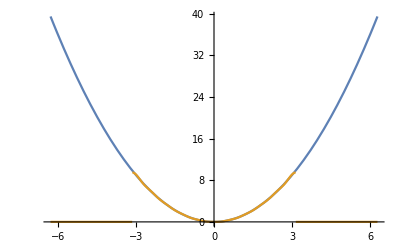

```mathematica
f1=x^2;
f1Fourier=FourierSeries[f1,x,10]
p[x_,left_,right_]:=HeavisideTheta[x-left] HeavisideTheta[right-x]
Plot[{f1 p[x,-2 Pi,2 Pi],f1Fourier p[x,-Pi,Pi]},{x,-2Pi,2Pi}]
```

```mathematica
(*Q2: find the Fourier series (basis {ⅇ^(ⅈ n x)/(√(2π))},n∈Integers) f2Fourier[x] of function f2[x] = Piecewise[{{Mod[x, 2 Pi, -Pi]+Pi,-Pi<Mod[x, 2 Pi, -Pi]<=0},{Mod[x, 2 Pi, -Pi], 0<Mod[x, 2 Pi, -Pi]<Pi}}] to the 20th order. And plot both functions together in the same plot with the range {t, -5 Pi, 5 Pi}.*}
```

-1/2 ⅈ ⅇ^(-2 ⅈ x)+1/2 ⅈ ⅇ^(2 ⅈ x)-1/4 ⅈ ⅇ^(-4 ⅈ x)+1/4 ⅈ ⅇ^(4 ⅈ x)-1/6 ⅈ ⅇ^(-6 ⅈ x)+1/6 ⅈ ⅇ^(6 ⅈ x)-1/8 ⅈ ⅇ^(-8 ⅈ x)+1/8 ⅈ ⅇ^(8 ⅈ x)-1/10 ⅈ ⅇ^(-10 ⅈ x)+1/10 ⅈ ⅇ^(10 ⅈ x)-1/12 ⅈ ⅇ^(-12 ⅈ x)+1/12 ⅈ ⅇ^(12 ⅈ x)-1/14 ⅈ ⅇ^(-14 ⅈ x)+1/14 ⅈ ⅇ^(14 ⅈ x)-1/16 ⅈ ⅇ^(-16 ⅈ x)+1/16 ⅈ ⅇ^(16 ⅈ x)-1/18 ⅈ ⅇ^(-18 ⅈ x)+1/18 ⅈ ⅇ^(18 ⅈ x)-1/20 ⅈ ⅇ^(-20 ⅈ x)+1/20 ⅈ ⅇ^(20 ⅈ x)+π/2

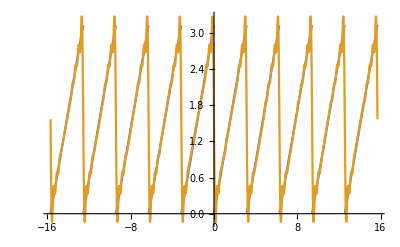

```mathematica
f2=Piecewise[{{Mod[x, 2 Pi, -Pi]+Pi,-Pi<Mod[x, 2 Pi, -Pi]<=0},{Mod[x, 2 Pi, -Pi], 0<Mod[x, 2 Pi, -Pi]<Pi}}];
f2Fourier=FourierSeries[f2,x,20]
Plot[{f2,f2Fourier},{x,-5 Pi, 5 Pi}]
```

```mathematica
(*Q3: f3[t]=Exp[-t^2] Sin[t]. Find the Fourier Transform f3Fourier[ω] of f3[t]. Can you plot f3Fourier[ω] with the range {ω, -3 Pi,3 Pi}? If not, explain why and plot Abs[f3Fourier[ω]] with the range {ω, -3 Pi,3 Pi}.*}
```

(ⅈ (-1+Cosh[ω]+Sinh[ω]) (Cosh[1/4 (1+ω)^2]-Sinh[1/4 (1+ω)^2]))/(2 √2)

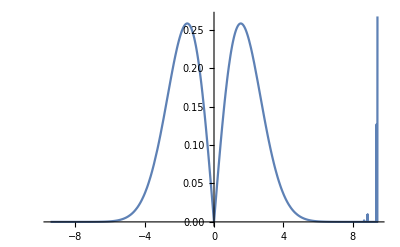

```mathematica
f3=Exp[-x^2] Sin[x];
f3Fourier=FourierTransform[f3,x,ω]
Plot[Abs[f3Fourier],{ω,-3 Pi,3Pi}]
(*Unable to plot the Fourier transformation without the absolute value because at some points there would be complex numbers involved which would be unable to be graphed on a standard x-y graph*)
```

```mathematica
(*Q4: Power spectrum of a damped sinusoid. Let's consider a damped sinusoid f4[t]=Sin[10 t]Exp[-t/2]UnitStep[t]. Plot f4 in the range {t, - Pi,Pi}. What is its Fourier transform f4Fourier[ω]? Plot Abs[f4Fourier] with the range {ω, 0, 40}, and use the "PlotRange→All" option in your plot. Can you identify the ω = 10 peak in the power spectrum? *}
```

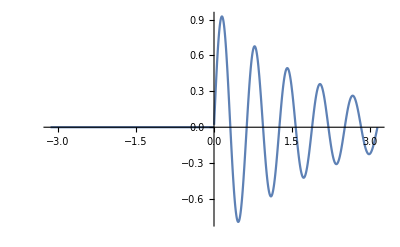

(20 √(2/π))/(401-4 ⅈ ω-4 ω^2)

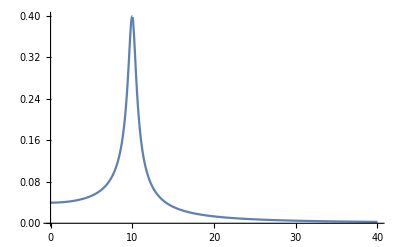

```mathematica
f4=Sin[10 x]Exp[-x/2]UnitStep[x];
Plot[f4,{x,-Pi,Pi}]
f4Fourier=FourierTransform[f4,x,ω]
Plot[Abs[f4Fourier],{ω,0,40},PlotRange->All]
(*The ω=10 peak is clearly seen at around 0.4*)
```

```mathematica
(*Q5: Consider the periodic function f5[x]={{0, -π<x<0}, {Sin[x], 0<x<π}}
  Find the Fourier trig series f5Fourier up to the 4th order. Then plot f5 and f5Fourier in the same plot with the range {x, -5 Pi, 5 Pi}.*}
```

1/4 ⅈ ⅇ^(-ⅈ x)-1/4 ⅈ ⅇ^(ⅈ x)+1/π-ⅇ^(-2 ⅈ x)/(3 π)-ⅇ^(2 ⅈ x)/(3 π)-ⅇ^(-4 ⅈ x)/(15 π)-ⅇ^(4 ⅈ x)/(15 π)

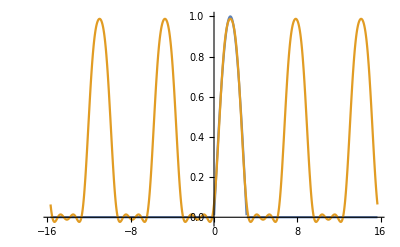

```mathematica
f5=Piecewise[{{0,-Pi<x<0},{Sin[x],0<x<Pi}}];
f5Fourier=FourierSeries[f5,x,4]
Plot[{f5,f5Fourier},{x,-5 Pi, 5 Pi}]
```

```mathematica
(*Q6: Period function not in the range of (-Pi, Pi): Find the first few terms of the Fourier trig series (f6Fourier) for the function f6[x]=x^2 for 0<x<2 π periodically repeated. Retain terms up to {Sin[5 x],Cos[5 x]}. Plot f6 and f6Fourier in the same plot with the range {x, -4Pi, 4Pi}*}
```

Piecewise[{{Mod[x,2 π,0]^2, 0<Mod[x,2 π,0]<2 π}, {0, True}}]

(4 π^2)/3+4 Cos[x]+Cos[2 x]+4/9 Cos[3 x]+1/4 Cos[4 x]+4/25 Cos[5 x]-4 π Sin[x]-2 π Sin[2 x]-4/3 π Sin[3 x]-π Sin[4 x]-4/5 π Sin[5 x]

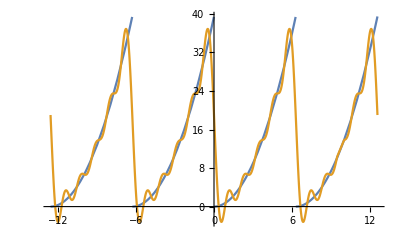

```mathematica
f6=Piecewise[{{(Mod[x,2Pi,0])^2,0<Mod[x,2Pi,0]<2Pi}}]
f6Fourier=FourierTrigSeries[f6,x,5]
Plot[{f6,f6Fourier},{x,-4Pi, 4Pi}]
```